# Combinatorics

Author Name

Abstract

## Section

XXXX:

## Binomial

There are 10 candidates who apply for a job. Four will be selected. How many ways can the president hire four new workers?

This is the binomial coefficient with n=10 and k=4 or n=10 and m=4.

```mathematica
Binomial[10,4]
```

210

There are 210 ways. This number is small enough that all the possible ways can be enumerated. Assign a color to each candidate and select subsets with length 4.

```mathematica
candidates=Take[ColorData[104,"ColorList"],10]
```

{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]}

```mathematica
Subsets[candidates,{4}]
```

{{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.627887, 0.708654, 0.],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913]},{RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]},{RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]}}

Find the length:

```mathematica
Length[Subsets[candidates,{4}]]
```

210

There are 48 candidates now and 40 will be hired. How many ways can 40 candidates be chosen? This is 48 choose 40, also written as (48
40)

```mathematica
Binomial[48,40]
```

377348994

Find the first 10 ways to choose 40 candidates by using numbers to represent candidates.

```mathematica
Subsets[Range[48],{40},10]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,42},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,43},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,44},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,45},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,46},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,47},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,48},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,40,41}}

There are five balls in a bag. I take a ball out and observe the color. I then replace the ball I took and repeat the experiment. How many distinct outcomes are possible if a ball, given the ball is replaced after the ball is removed from the bag?

```mathematica
With[{n=5,m=2},Tuples[Range[n],{m}]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

We only care about distinct balls, so {4,4} simplifies to {4} for example. {4,2} and {2,4} are also equivalent. We don't care about order.

```mathematica
Sort/@With[{n=5,m=2},Tuples[Range[n],{m}]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,2},{2,2},{2,3},{2,4},{2,5},{1,3},{2,3},{3,3},{3,4},{3,5},{1,4},{2,4},{3,4},{4,4},{4,5},{1,5},{2,5},{3,5},{4,5},{5,5}}

```mathematica
DeleteDuplicates[Sort/@With[{n=5,m=2},Tuples[Range[n],{m}]]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,2},{2,3},{2,4},{2,5},{3,3},{3,4},{3,5},{4,4},{4,5},{5,5}}

```mathematica
Length[DeleteDuplicates[Sort/@With[{n=5,m=2},Tuples[Range[n],{m}]]]]
```

15

This is Binomial[m+n-1, m].

```mathematica
With[{n=5,m=2},Binomial[m+n-1,m]]
```

15

There are 48 balls and we select 40. How many distinct samples with replacement are possible?

```mathematica
With[{n=48,m=40},Binomial[m+n-1,m]]
```

9988677302355003038019660

How many ways are there to arrange 5 cows and 2 horses?

There are Binomial[m+n, m] ways to arrange n indistinguishable objects of one kind, and m indistinguishable objects of another kind:

```mathematica
With[{n=5,m=2},Binomial[n+m,m]]
```

21

There are 21 ways to arrange 5 cows and 2 horses.

```mathematica
With[{n=5,m=2},Permutations[Join[ConstantArray[0,n],ConstantArray[1,m]]]]
```

{{0,0,0,0,0,1,1},{0,0,0,0,1,0,1},{0,0,0,0,1,1,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,0},{0,0,0,1,1,0,0},{0,0,1,0,0,0,1},{0,0,1,0,0,1,0},{0,0,1,0,1,0,0},{0,0,1,1,0,0,0},{0,1,0,0,0,0,1},{0,1,0,0,0,1,0},{0,1,0,0,1,0,0},{0,1,0,1,0,0,0},{0,1,1,0,0,0,0},{1,0,0,0,0,0,1},{1,0,0,0,0,1,0},{1,0,0,0,1,0,0},{1,0,0,1,0,0,0},{1,0,1,0,0,0,0},{1,1,0,0,0,0,0}}

```mathematica
Length[With[{n=5,m=2},Permutations[Join[ConstantArray[0,n],ConstantArray[1,m]]]]]
```

21

There are 5 cows, 2 horses and 3 donkeys. How many ways are there to arrange the cows, horses, and donkeys?

```mathematica
With[{n=5,m=2,m1=3},Permutations[Join[ConstantArray[0,n],ConstantArray[1,m],ConstantArray[2,m1]]]]
```

```mathematica
Length[With[{n=5,m=2,m1=3},Permutations[Join[ConstantArray[0,n],ConstantArray[1,m],ConstantArray[2,m1]]]]]
```

2520

This is the multinomial coefficient, ((n_1+n_2+n_3)!)/(n_1!n_2!n_3!). The multinomial coefficient gives the number of ways of partitioning N distinct objects into m sets, each of size n_i (with N=∑_(i=1)^m n_i).

```mathematica
Multinomial[5,3,2]
```

2520

There are 10 cows, 4 oxen, 3 geese, 6 ducks, 5 chickens, 6 donkeys, 4 oxen, 4 water buffalo and 6 sheep. How many ways are there to arrange the animals.

```mathematica
Multinomial[10,4,3,6,5,6,4,4,6]
```

920835479918927720789697275746606080000

There are 6 people in 6 chairs numbered from 1 to 6. how many ways are there where every person moves to a new chair? This is a question for how many derangements are there with n=6 items. The nth subfactorial (also called the derangement number; Goulden and Jackson 1983, p. 48; Graham et al. 2003, p. 1050) is the number of permutations of n objects in which no object appears in its natural place. The subfactorial of n is written !n.

```mathematica
Subfactorial[6]
```

265

Find all the permutations:

```mathematica
Permutations[Range[4]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
DeleteCases[Permutations[Range[4]],{1,__}|{_,2,__}|{__,3,_}|{__,4}]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

```mathematica
Length[DeleteCases[Permutations[Range[4]],{1,__}|{_,2,__}|{__,3,_}|{__,4}]]
```

9

derangements with 3 items.

```mathematica
Permutations[Range[3]]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
DeleteCases[Permutations[Range[3]],{1,__}|{_,2,__}|{__,3}]
```

{{2,3,1},{3,1,2}}

```mathematica
Length[DeleteCases[Permutations[Range[3]],{1,__}|{_,2,__}|{__,3}]]
```

2

find the subfactorial:

```mathematica
Subfactorial[3]
```

2

derangements with 5 items:

```mathematica
Permutations[Range[5]]//Short
```

{{1,2,3,4,5},{1,2,3,5,4},{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4},«110»,{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1},{5,4,3,1,2},{5,4,3,2,1}}

```mathematica
DeleteCases[Permutations[Range[5]],{1,__}|{_,2,__}|{__,3__}|{__,4,_}|{__,5}]
```

{{2,1,3,5,4},{2,1,4,5,3},{2,1,5,3,4},{2,3,1,5,4},{2,3,4,5,1},{2,3,5,1,4},{2,4,1,5,3},{2,4,3,5,1},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,3,1,4},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,5,4},{3,1,4,5,2},{3,1,5,2,4},{3,4,1,5,2},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,2,1,4},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,5,3},{4,1,3,5,2},{4,1,5,2,3},{4,1,5,3,2},{4,3,1,5,2},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{4,5,3,1,2},{4,5,3,2,1},{5,1,2,3,4},{5,1,3,2,4},{5,1,4,2,3},{5,1,4,3,2},{5,3,1,2,4},{5,3,2,1,4},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1},{5,4,3,1,2},{5,4,3,2,1}}

```mathematica
Length[DeleteCases[Permutations[Range[5]],{1,__}|{_,2,__}|{__,3__}|{__,4,_}|{__,5}]]
```

53

```mathematica
Subfactorial[5]
```

44

```mathematica
Length[DeleteCases[Permutations[Range[4]],{1,Repeated[_,{3}]}|{_,2,__}|{__,3,_}|{__,4}]]
```

9

```mathematica
DeleteCases[Permutations[Range[4]],{1,__}|{_,2,__}|{__,3,_}|{__,4}]
```

```mathematica
Length[DeleteCases[Permutations[Range[5]],{1,Repeated[_,{4}]}|{Repeated[_,{1}],2,Repeated[_,{3}]}|{Repeated[_,{2}],3,Repeated[_,{2}]}|{Repeated[_,{3}],4,Repeated[_,{1}]}|{Repeated[_,{4}],5}]]
```

44

```mathematica
DeleteCases[Permutations[Range[5]],{1,Repeated[_,{4}]}|{Repeated[_,{1}],2,Repeated[_,{3}]}|{Repeated[_,{2}],3,Repeated[_,{2}]}|{Repeated[_,{3}],4,Repeated[_,{1}]}|{Repeated[_,{4}],5}]
```

{{2,1,4,5,3},{2,1,5,3,4},{2,3,1,5,4},{2,3,4,5,1},{2,3,5,1,4},{2,4,1,5,3},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,5,4},{3,1,4,5,2},{3,1,5,2,4},{3,4,1,5,2},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,2,1,4},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,5,3},{4,1,5,2,3},{4,1,5,3,2},{4,3,1,5,2},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{5,1,2,3,4},{5,1,4,2,3},{5,1,4,3,2},{5,3,1,2,4},{5,3,2,1,4},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1}}

```mathematica
DeleteCases[Permutations[Range[6]],{1,Repeated[_,{5}]}|{Repeated[_,{1}],2,Repeated[_,{4}]}|{Repeated[_,{2}],3,Repeated[_,{3}]}|{Repeated[_,{3}],4,Repeated[_,{2}]}|{Repeated[_,{4}],5,Repeated[_,{1}]}|{Repeated[_,{5}],6}]
```

{{2,1,4,3,6,5},{2,1,4,5,6,3},{2,1,4,6,3,5},{2,1,5,3,6,4},{2,1,5,6,3,4},{2,1,5,6,4,3},{2,1,6,3,4,5},{2,1,6,5,3,4},{2,1,6,5,4,3},{2,3,1,5,6,4},{2,3,1,6,4,5},{2,3,4,1,6,5},{2,3,4,5,6,1},{2,3,4,6,1,5},{2,3,5,1,6,4},{2,3,5,6,1,4},{2,3,5,6,4,1},{2,3,6,1,4,5},{2,3,6,5,1,4},{2,3,6,5,4,1},{2,4,1,3,6,5},{2,4,1,5,6,3},{2,4,1,6,3,5},{2,4,5,1,6,3},{2,4,5,3,6,1},{2,4,5,6,1,3},{2,4,5,6,3,1},{2,4,6,1,3,5},{2,4,6,3,1,5},{2,4,6,5,1,3},{2,4,6,5,3,1},{2,5,1,3,6,4},{2,5,1,6,3,4},{2,5,1,6,4,3},{2,5,4,1,6,3},{2,5,4,3,6,1},{2,5,4,6,1,3},{2,5,4,6,3,1},{2,5,6,1,3,4},{2,5,6,1,4,3},{2,5,6,3,1,4},{2,5,6,3,4,1},{2,6,1,3,4,5},{2,6,1,5,3,4},{2,6,1,5,4,3},{2,6,4,1,3,5},{2,6,4,3,1,5},{2,6,4,5,1,3},{2,6,4,5,3,1},{2,6,5,1,3,4},{2,6,5,1,4,3},{2,6,5,3,1,4},{2,6,5,3,4,1},{3,1,2,5,6,4},{3,1,2,6,4,5},{3,1,4,2,6,5},{3,1,4,5,6,2},{3,1,4,6,2,5},{3,1,5,2,6,4},{3,1,5,6,2,4},{3,1,5,6,4,2},{3,1,6,2,4,5},{3,1,6,5,2,4},{3,1,6,5,4,2},{3,4,1,2,6,5},{3,4,1,5,6,2},{3,4,1,6,2,5},{3,4,2,1,6,5},{3,4,2,5,6,1},{3,4,2,6,1,5},{3,4,5,1,6,2},{3,4,5,2,6,1},{3,4,5,6,1,2},{3,4,5,6,2,1},{3,4,6,1,2,5},{3,4,6,2,1,5},{3,4,6,5,1,2},{3,4,6,5,2,1},{3,5,1,2,6,4},{3,5,1,6,2,4},{3,5,1,6,4,2},{3,5,2,1,6,4},{3,5,2,6,1,4},{3,5,2,6,4,1},{3,5,4,1,6,2},{3,5,4,2,6,1},{3,5,4,6,1,2},{3,5,4,6,2,1},{3,5,6,1,2,4},{3,5,6,1,4,2},{3,5,6,2,1,4},{3,5,6,2,4,1},{3,6,1,2,4,5},{3,6,1,5,2,4},{3,6,1,5,4,2},{3,6,2,1,4,5},{3,6,2,5,1,4},{3,6,2,5,4,1},{3,6,4,1,2,5},{3,6,4,2,1,5},{3,6,4,5,1,2},{3,6,4,5,2,1},{3,6,5,1,2,4},{3,6,5,1,4,2},{3,6,5,2,1,4},{3,6,5,2,4,1},{4,1,2,3,6,5},{4,1,2,5,6,3},{4,1,2,6,3,5},{4,1,5,2,6,3},{4,1,5,3,6,2},{4,1,5,6,2,3},{4,1,5,6,3,2},{4,1,6,2,3,5},{4,1,6,3,2,5},{4,1,6,5,2,3},{4,1,6,5,3,2},{4,3,1,2,6,5},{4,3,1,5,6,2},{4,3,1,6,2,5},{4,3,2,1,6,5},{4,3,2,5,6,1},{4,3,2,6,1,5},{4,3,5,1,6,2},{4,3,5,2,6,1},{4,3,5,6,1,2},{4,3,5,6,2,1},{4,3,6,1,2,5},{4,3,6,2,1,5},{4,3,6,5,1,2},{4,3,6,5,2,1},{4,5,1,2,6,3},{4,5,1,3,6,2},{4,5,1,6,2,3},{4,5,1,6,3,2},{4,5,2,1,6,3},{4,5,2,3,6,1},{4,5,2,6,1,3},{4,5,2,6,3,1},{4,5,6,1,2,3},{4,5,6,1,3,2},{4,5,6,2,1,3},{4,5,6,2,3,1},{4,5,6,3,1,2},{4,5,6,3,2,1},{4,6,1,2,3,5},{4,6,1,3,2,5},{4,6,1,5,2,3},{4,6,1,5,3,2},{4,6,2,1,3,5},{4,6,2,3,1,5},{4,6,2,5,1,3},{4,6,2,5,3,1},{4,6,5,1,2,3},{4,6,5,1,3,2},{4,6,5,2,1,3},{4,6,5,2,3,1},{4,6,5,3,1,2},{4,6,5,3,2,1},{5,1,2,3,6,4},{5,1,2,6,3,4},{5,1,2,6,4,3},{5,1,4,2,6,3},{5,1,4,3,6,2},{5,1,4,6,2,3},{5,1,4,6,3,2},{5,1,6,2,3,4},{5,1,6,2,4,3},{5,1,6,3,2,4},{5,1,6,3,4,2},{5,3,1,2,6,4},{5,3,1,6,2,4},{5,3,1,6,4,2},{5,3,2,1,6,4},{5,3,2,6,1,4},{5,3,2,6,4,1},{5,3,4,1,6,2},{5,3,4,2,6,1},{5,3,4,6,1,2},{5,3,4,6,2,1},{5,3,6,1,2,4},{5,3,6,1,4,2},{5,3,6,2,1,4},{5,3,6,2,4,1},{5,4,1,2,6,3},{5,4,1,3,6,2},{5,4,1,6,2,3},{5,4,1,6,3,2},{5,4,2,1,6,3},{5,4,2,3,6,1},{5,4,2,6,1,3},{5,4,2,6,3,1},{5,4,6,1,2,3},{5,4,6,1,3,2},{5,4,6,2,1,3},{5,4,6,2,3,1},{5,4,6,3,1,2},{5,4,6,3,2,1},{5,6,1,2,3,4},{5,6,1,2,4,3},{5,6,1,3,2,4},{5,6,1,3,4,2},{5,6,2,1,3,4},{5,6,2,1,4,3},{5,6,2,3,1,4},{5,6,2,3,4,1},{5,6,4,1,2,3},{5,6,4,1,3,2},{5,6,4,2,1,3},{5,6,4,2,3,1},{5,6,4,3,1,2},{5,6,4,3,2,1},{6,1,2,3,4,5},{6,1,2,5,3,4},{6,1,2,5,4,3},{6,1,4,2,3,5},{6,1,4,3,2,5},{6,1,4,5,2,3},{6,1,4,5,3,2},{6,1,5,2,3,4},{6,1,5,2,4,3},{6,1,5,3,2,4},{6,1,5,3,4,2},{6,3,1,2,4,5},{6,3,1,5,2,4},{6,3,1,5,4,2},{6,3,2,1,4,5},{6,3,2,5,1,4},{6,3,2,5,4,1},{6,3,4,1,2,5},{6,3,4,2,1,5},{6,3,4,5,1,2},{6,3,4,5,2,1},{6,3,5,1,2,4},{6,3,5,1,4,2},{6,3,5,2,1,4},{6,3,5,2,4,1},{6,4,1,2,3,5},{6,4,1,3,2,5},{6,4,1,5,2,3},{6,4,1,5,3,2},{6,4,2,1,3,5},{6,4,2,3,1,5},{6,4,2,5,1,3},{6,4,2,5,3,1},{6,4,5,1,2,3},{6,4,5,1,3,2},{6,4,5,2,1,3},{6,4,5,2,3,1},{6,4,5,3,1,2},{6,4,5,3,2,1},{6,5,1,2,3,4},{6,5,1,2,4,3},{6,5,1,3,2,4},{6,5,1,3,4,2},{6,5,2,1,3,4},{6,5,2,1,4,3},{6,5,2,3,1,4},{6,5,2,3,4,1},{6,5,4,1,2,3},{6,5,4,1,3,2},{6,5,4,2,1,3},{6,5,4,2,3,1},{6,5,4,3,1,2},{6,5,4,3,2,1}}

```mathematica
Length[DeleteCases[Permutations[Range[6]],{1,Repeated[_,{5}]}|{Repeated[_,{1}],2,Repeated[_,{4}]}|{Repeated[_,{2}],3,Repeated[_,{3}]}|{Repeated[_,{3}],4,Repeated[_,{2}]}|{Repeated[_,{4}],5,Repeated[_,{1}]}|{Repeated[_,{5}],6}]]
```

265

```mathematica
Subfactorial[6]
```

265

Use the resourcefunction Derangements:

```mathematica
PersistResourceFunction["Derangements"]
```

Success[…]

```mathematica
Derangements[6]
```

{{2,1,4,3,6,5},{2,1,4,5,6,3},{2,1,4,6,3,5},{2,1,5,3,6,4},{2,1,5,6,3,4},{2,1,5,6,4,3},{2,1,6,3,4,5},{2,1,6,5,3,4},{2,1,6,5,4,3},{2,3,1,5,6,4},{2,3,1,6,4,5},{2,3,4,1,6,5},{2,3,4,5,6,1},{2,3,4,6,1,5},{2,3,5,1,6,4},{2,3,5,6,1,4},{2,3,5,6,4,1},{2,3,6,1,4,5},{2,3,6,5,1,4},{2,3,6,5,4,1},{2,4,1,3,6,5},{2,4,1,5,6,3},{2,4,1,6,3,5},{2,4,5,1,6,3},{2,4,5,3,6,1},{2,4,5,6,1,3},{2,4,5,6,3,1},{2,4,6,1,3,5},{2,4,6,3,1,5},{2,4,6,5,1,3},{2,4,6,5,3,1},{2,5,1,3,6,4},{2,5,1,6,3,4},{2,5,1,6,4,3},{2,5,4,1,6,3},{2,5,4,3,6,1},{2,5,4,6,1,3},{2,5,4,6,3,1},{2,5,6,1,3,4},{2,5,6,1,4,3},{2,5,6,3,1,4},{2,5,6,3,4,1},{2,6,1,3,4,5},{2,6,1,5,3,4},{2,6,1,5,4,3},{2,6,4,1,3,5},{2,6,4,3,1,5},{2,6,4,5,1,3},{2,6,4,5,3,1},{2,6,5,1,3,4},{2,6,5,1,4,3},{2,6,5,3,1,4},{2,6,5,3,4,1},{3,1,2,5,6,4},{3,1,2,6,4,5},{3,1,4,2,6,5},{3,1,4,5,6,2},{3,1,4,6,2,5},{3,1,5,2,6,4},{3,1,5,6,2,4},{3,1,5,6,4,2},{3,1,6,2,4,5},{3,1,6,5,2,4},{3,1,6,5,4,2},{3,4,1,2,6,5},{3,4,1,5,6,2},{3,4,1,6,2,5},{3,4,2,1,6,5},{3,4,2,5,6,1},{3,4,2,6,1,5},{3,4,5,1,6,2},{3,4,5,2,6,1},{3,4,5,6,1,2},{3,4,5,6,2,1},{3,4,6,1,2,5},{3,4,6,2,1,5},{3,4,6,5,1,2},{3,4,6,5,2,1},{3,5,1,2,6,4},{3,5,1,6,2,4},{3,5,1,6,4,2},{3,5,2,1,6,4},{3,5,2,6,1,4},{3,5,2,6,4,1},{3,5,4,1,6,2},{3,5,4,2,6,1},{3,5,4,6,1,2},{3,5,4,6,2,1},{3,5,6,1,2,4},{3,5,6,1,4,2},{3,5,6,2,1,4},{3,5,6,2,4,1},{3,6,1,2,4,5},{3,6,1,5,2,4},{3,6,1,5,4,2},{3,6,2,1,4,5},{3,6,2,5,1,4},{3,6,2,5,4,1},{3,6,4,1,2,5},{3,6,4,2,1,5},{3,6,4,5,1,2},{3,6,4,5,2,1},{3,6,5,1,2,4},{3,6,5,1,4,2},{3,6,5,2,1,4},{3,6,5,2,4,1},{4,1,2,3,6,5},{4,1,2,5,6,3},{4,1,2,6,3,5},{4,1,5,2,6,3},{4,1,5,3,6,2},{4,1,5,6,2,3},{4,1,5,6,3,2},{4,1,6,2,3,5},{4,1,6,3,2,5},{4,1,6,5,2,3},{4,1,6,5,3,2},{4,3,1,2,6,5},{4,3,1,5,6,2},{4,3,1,6,2,5},{4,3,2,1,6,5},{4,3,2,5,6,1},{4,3,2,6,1,5},{4,3,5,1,6,2},{4,3,5,2,6,1},{4,3,5,6,1,2},{4,3,5,6,2,1},{4,3,6,1,2,5},{4,3,6,2,1,5},{4,3,6,5,1,2},{4,3,6,5,2,1},{4,5,1,2,6,3},{4,5,1,3,6,2},{4,5,1,6,2,3},{4,5,1,6,3,2},{4,5,2,1,6,3},{4,5,2,3,6,1},{4,5,2,6,1,3},{4,5,2,6,3,1},{4,5,6,1,2,3},{4,5,6,1,3,2},{4,5,6,2,1,3},{4,5,6,2,3,1},{4,5,6,3,1,2},{4,5,6,3,2,1},{4,6,1,2,3,5},{4,6,1,3,2,5},{4,6,1,5,2,3},{4,6,1,5,3,2},{4,6,2,1,3,5},{4,6,2,3,1,5},{4,6,2,5,1,3},{4,6,2,5,3,1},{4,6,5,1,2,3},{4,6,5,1,3,2},{4,6,5,2,1,3},{4,6,5,2,3,1},{4,6,5,3,1,2},{4,6,5,3,2,1},{5,1,2,3,6,4},{5,1,2,6,3,4},{5,1,2,6,4,3},{5,1,4,2,6,3},{5,1,4,3,6,2},{5,1,4,6,2,3},{5,1,4,6,3,2},{5,1,6,2,3,4},{5,1,6,2,4,3},{5,1,6,3,2,4},{5,1,6,3,4,2},{5,3,1,2,6,4},{5,3,1,6,2,4},{5,3,1,6,4,2},{5,3,2,1,6,4},{5,3,2,6,1,4},{5,3,2,6,4,1},{5,3,4,1,6,2},{5,3,4,2,6,1},{5,3,4,6,1,2},{5,3,4,6,2,1},{5,3,6,1,2,4},{5,3,6,1,4,2},{5,3,6,2,1,4},{5,3,6,2,4,1},{5,4,1,2,6,3},{5,4,1,3,6,2},{5,4,1,6,2,3},{5,4,1,6,3,2},{5,4,2,1,6,3},{5,4,2,3,6,1},{5,4,2,6,1,3},{5,4,2,6,3,1},{5,4,6,1,2,3},{5,4,6,1,3,2},{5,4,6,2,1,3},{5,4,6,2,3,1},{5,4,6,3,1,2},{5,4,6,3,2,1},{5,6,1,2,3,4},{5,6,1,2,4,3},{5,6,1,3,2,4},{5,6,1,3,4,2},{5,6,2,1,3,4},{5,6,2,1,4,3},{5,6,2,3,1,4},{5,6,2,3,4,1},{5,6,4,1,2,3},{5,6,4,1,3,2},{5,6,4,2,1,3},{5,6,4,2,3,1},{5,6,4,3,1,2},{5,6,4,3,2,1},{6,1,2,3,4,5},{6,1,2,5,3,4},{6,1,2,5,4,3},{6,1,4,2,3,5},{6,1,4,3,2,5},{6,1,4,5,2,3},{6,1,4,5,3,2},{6,1,5,2,3,4},{6,1,5,2,4,3},{6,1,5,3,2,4},{6,1,5,3,4,2},{6,3,1,2,4,5},{6,3,1,5,2,4},{6,3,1,5,4,2},{6,3,2,1,4,5},{6,3,2,5,1,4},{6,3,2,5,4,1},{6,3,4,1,2,5},{6,3,4,2,1,5},{6,3,4,5,1,2},{6,3,4,5,2,1},{6,3,5,1,2,4},{6,3,5,1,4,2},{6,3,5,2,1,4},{6,3,5,2,4,1},{6,4,1,2,3,5},{6,4,1,3,2,5},{6,4,1,5,2,3},{6,4,1,5,3,2},{6,4,2,1,3,5},{6,4,2,3,1,5},{6,4,2,5,1,3},{6,4,2,5,3,1},{6,4,5,1,2,3},{6,4,5,1,3,2},{6,4,5,2,1,3},{6,4,5,2,3,1},{6,4,5,3,1,2},{6,4,5,3,2,1},{6,5,1,2,3,4},{6,5,1,2,4,3},{6,5,1,3,2,4},{6,5,1,3,4,2},{6,5,2,1,3,4},{6,5,2,1,4,3},{6,5,2,3,1,4},{6,5,2,3,4,1},{6,5,4,1,2,3},{6,5,4,1,3,2},{6,5,4,2,1,3},{6,5,4,2,3,1},{6,5,4,3,1,2},{6,5,4,3,2,1}}

Compute the number of different ways to parenthesize an expression:

```mathematica
SetAttributes[f,{Flat,OneIdentity}]
```

Distribute over lists in CirclePluspaclet:ref/CirclePlus:

```mathematica
e:CirclePlus[___,_List,___]:=Distribute[Unevaluated[e],List]
```

Use the pattern matcher to repeatedly split the list into two parts in all possible ways:

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{a⊕(b⊕(c⊕d)),a⊕((b⊕c)⊕d),(a⊕b)⊕(c⊕d),(a⊕(b⊕c))⊕d,((a⊕b)⊕c)⊕d}

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{a⊕(b⊕(c⊕d)),a⊕((b⊕c)⊕d),(a⊕b)⊕(c⊕d),(a⊕(b⊕c))⊕d,((a⊕b)⊕c)⊕d}

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten
```

{a⊕(b⊕(c⊕d)),a⊕((b⊕c)⊕d),(a⊕b)⊕(c⊕d),(a⊕(b⊕c))⊕d,((a⊕b)⊕c)⊕d}

```mathematica
Length[parenthesizedlist]
```

5

```mathematica
ExpressionTree[a⊕(b⊕(c⊕d))]
```

-Graphics-

```mathematica
ToString/@parenthesizedlist
```

{a ⊕ (b ⊕ (c ⊕ d)),a ⊕ ((b ⊕ c) ⊕ d),(a ⊕ b) ⊕ (c ⊕ d),(a ⊕ (b ⊕ c)) ⊕ d,((a ⊕ b) ⊕ c) ⊕ d}

```mathematica
StringDelete["a ⊕ (b ⊕ (c ⊕ d))",x_/;!StringMatchQ[x,"("|")"]]
```

(())

```mathematica
StringDelete[ToString[#],x_/;!StringMatchQ[x,"("|")"]]&/@parenthesizedlist
```

{(()),(()),()(),(()),(())}

```mathematica
DeleteDuplicates[StringDelete[ToString[#],x_/;!StringMatchQ[x,"("|")"]]&/@(f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten)]
```

{(()),()()}

```mathematica
DeleteDuplicates[StringDelete[ToString[#],x_/;!StringMatchQ[x,"("|")"]]&/@(f[Sequence@@{a,b,c,d}]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten)]
```

{(()),()()}

```mathematica
DeleteDuplicates[StringDelete[ToString[#],x_/;!StringMatchQ[x,"("|")"]]&/@(f[Sequence@@Array[Indexed[x,##]&,2 3]]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CirclePlus[u,v]]}//Flatten)]
```

{(((()))),((()())),(()(())),((())()),()((())),()(()()),(())(()),((()))(),(()())()}

```mathematica
DeleteDuplicates[StringDelete[ToString[#],x_/;!StringMatchQ[x,"("|")"]]&/@parenthesizedlist]
```

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>CircleDot[u,v]]}//Flatten/.
```

The number of ways to parenthesize the expression a⊕b⊕c⊕d:

```mathematica
Length[parenthesizedlist]
```

5

Check:

```mathematica
CatalanNumber[3]
```

5

```mathematica
parenthesizedlist
```

{a⊕(b⊕(c⊕d)),a⊕((b⊕c)⊕d),(a⊕b)⊕(c⊕d),(a⊕(b⊕c))⊕d,((a⊕b)⊕c)⊕d}

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>Power[u,v]]}//Flatten
```

{a^(b^(c^d)),a^((b^c)^d),(a^b)^(c^d),(a^(b^c))^d,((a^b)^c)^d}

```mathematica
{a,b,c,d}=Range[2,5]
```

{2,3,4,5}

```mathematica
parenthesizedlist
```

{1,1,1,1,1}

```mathematica
Table[Table[CatalanNumber[i+j]+CatalanNumber[i+j+1],{i,0,n-1},{j,0,n-1}],{n,10}]
```

{{{2}},{{2,3},{3,7}},{{2,3,7},{3,7,19},{7,19,56}},{{2,3,7,19},{3,7,19,56},{7,19,56,174},{19,56,174,561}},{{2,3,7,19,56},{3,7,19,56,174},{7,19,56,174,561},{19,56,174,561,1859},{56,174,561,1859,6292}},{{2,3,7,19,56,174},{3,7,19,56,174,561},{7,19,56,174,561,1859},{19,56,174,561,1859,6292},{56,174,561,1859,6292,21658},{174,561,1859,6292,21658,75582}},{{2,3,7,19,56,174,561},{3,7,19,56,174,561,1859},{7,19,56,174,561,1859,6292},{19,56,174,561,1859,6292,21658},{56,174,561,1859,6292,21658,75582},{174,561,1859,6292,21658,75582,266798},{561,1859,6292,21658,75582,266798,950912}},{{2,3,7,19,56,174,561,1859},{3,7,19,56,174,561,1859,6292},{7,19,56,174,561,1859,6292,21658},{19,56,174,561,1859,6292,21658,75582},{56,174,561,1859,6292,21658,75582,266798},{174,561,1859,6292,21658,75582,266798,950912},{561,1859,6292,21658,75582,266798,950912,3417340},{1859,6292,21658,75582,266798,950912,3417340,12369285}},{{2,3,7,19,56,174,561,1859,6292},{3,7,19,56,174,561,1859,6292,21658},{7,19,56,174,561,1859,6292,21658,75582},{19,56,174,561,1859,6292,21658,75582,266798},{56,174,561,1859,6292,21658,75582,266798,950912},{174,561,1859,6292,21658,75582,266798,950912,3417340},{561,1859,6292,21658,75582,266798,950912,3417340,12369285},{1859,6292,21658,75582,266798,950912,3417340,12369285,45052515},{6292,21658,75582,266798,950912,3417340,12369285,45052515,165002460}},{{2,3,7,19,56,174,561,1859,6292,21658},{3,7,19,56,174,561,1859,6292,21658,75582},{7,19,56,174,561,1859,6292,21658,75582,266798},{19,56,174,561,1859,6292,21658,75582,266798,950912},{56,174,561,1859,6292,21658,75582,266798,950912,3417340},{174,561,1859,6292,21658,75582,266798,950912,3417340,12369285},{561,1859,6292,21658,75582,266798,950912,3417340,12369285,45052515},{1859,6292,21658,75582,266798,950912,3417340,12369285,45052515,165002460},{6292,21658,75582,266798,950912,3417340,12369285,45052515,165002460,607283490},{21658,75582,266798,950912,3417340,12369285,45052515,165002460,607283490,2244901890}}}

```mathematica
MatrixForm/@Table[Table[CatalanNumber[i+j]+CatalanNumber[i+j+1],{i,0,n-1},{j,0,n-1}],{n,10}]
```

{(2),(2 | 3
3 | 7),(2 | 3 | 7
3 | 7 | 19
7 | 19 | 56),(2 | 3 | 7 | 19
3 | 7 | 19 | 56
7 | 19 | 56 | 174
19 | 56 | 174 | 561),(2 | 3 | 7 | 19 | 56
3 | 7 | 19 | 56 | 174
7 | 19 | 56 | 174 | 561
19 | 56 | 174 | 561 | 1859
56 | 174 | 561 | 1859 | 6292),(2 | 3 | 7 | 19 | 56 | 174
3 | 7 | 19 | 56 | 174 | 561
7 | 19 | 56 | 174 | 561 | 1859
19 | 56 | 174 | 561 | 1859 | 6292
56 | 174 | 561 | 1859 | 6292 | 21658
174 | 561 | 1859 | 6292 | 21658 | 75582),(2 | 3 | 7 | 19 | 56 | 174 | 561
3 | 7 | 19 | 56 | 174 | 561 | 1859
7 | 19 | 56 | 174 | 561 | 1859 | 6292
19 | 56 | 174 | 561 | 1859 | 6292 | 21658
56 | 174 | 561 | 1859 | 6292 | 21658 | 75582
174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798
561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912),(2 | 3 | 7 | 19 | 56 | 174 | 561 | 1859
3 | 7 | 19 | 56 | 174 | 561 | 1859 | 6292
7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658
19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582
56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798
174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912
561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340
1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285),(2 | 3 | 7 | 19 | 56 | 174 | 561 | 1859 | 6292
3 | 7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658
7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582
19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798
56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912
174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340
561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285
1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515
6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515 | 165002460),(2 | 3 | 7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658
3 | 7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582
7 | 19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798
19 | 56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912
56 | 174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340
174 | 561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285
561 | 1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515
1859 | 6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515 | 165002460
6292 | 21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515 | 165002460 | 607283490
21658 | 75582 | 266798 | 950912 | 3417340 | 12369285 | 45052515 | 165002460 | 607283490 | 2244901890)}

```mathematica
parenthesizedlist=f[a,b,c,d]//.{f[x__]:>ReplaceList[f[x],f[u_,v_]:>h[u,v]]}//Flatten
```

{h[a,{h[b,{h[c,d]}],h[{h[b,c]},d]}],h[{h[a,b]},{h[c,d]}],h[{h[a,{h[b,c]}],h[{h[a,b]},c]},d]}

## Math functions

```mathematica
IntegerPart[2.4]
```

2

```mathematica
FractionalPart[2.4]
```

0.4

```mathematica
Round[2.4]
```

2

```mathematica
Floor[2.4]
```

2

```mathematica
Ceiling[2.4]
```

3

```mathematica
⌊2.4⌋
```

2

```mathematica
⌈2.4⌉
```

3

```mathematica
Rationalize[2.4]
```

12/5

```mathematica
Rationalize[2.4,10]
```

2

```mathematica
Rationalize[2.4,0.0010]
```

12/5

```mathematica
Rationalize[2.71828,0.001]
```

87/32

```mathematica
Rationalize[2.71828,0.0001]
```

193/71

```mathematica
IntegerPart[-3.4]
```

-3

```mathematica
FractionalPart[-3.4]
```

-0.4

```mathematica
FractionalPart[0]
```

0

```mathematica
Round[2.4]
```

2

```mathematica
Round[2.4]
```

2

```mathematica
Round[2.6]
```

3

```mathematica
Round[-2.4]
```

-2

```mathematica
Round[-2.5]
```

-2

```mathematica
Round[-2.6]
```

-3

```mathematica
⌊-2.5⌋
```

-3

```mathematica
RealSign[2.4]
```

1

```mathematica
RealSign[-2.4]
```

-1

```mathematica
RealSign[0]
```

0

```mathematica
UnitStep[2.3]
```

1

```mathematica
UnitStep[0]
```

1

```mathematica
UnitStep[-0.]
```

1

```mathematica
UnitStep[-0.1]
```

0

```mathematica
FunctionRange[UnitStep[x],x]
```

FunctionRange[UnitStep[x],x]

```mathematica
?FunctionRange
```

```mathematica
FunctionRange[y=UnitStep[x],x,y]
```

UnitStep[x]==0||UnitStep[x]==1

```mathematica
RealAbs[4.4]
```

4.4

```mathematica
RealAbs[-4.4]
```

4.4

```mathematica
Clip[4.4]
```

1

```mathematica
Clip[-2]
```

-1

```mathematica
Re[RandomComplex[]]
```

0.375411

```mathematica
SeedRandom[100];RandomReal[]
IntegerPart[RandomReal[]]
Round[RandomReal[]]
Floor[RandomReal[]]
```

0.0128701

0

0

0

```mathematica
SeedRandom[100];
BlockRandom[{RandomComplex[]}]
Re[RandomComplex[]]
RandomComplex[]
```

{0.0128701+0.338655 ⅈ}

0.0128701

0.223215+0.694454 ⅈ

```mathematica
Re[RandomComplex[]]
```

0.760978

```mathematica
Im[RandomComplex[]]
```

0.916096

```mathematica
Conjugate[RandomComplex[]]
```

0.307464-0.260418 ⅈ

```mathematica
Abs[RandomComplex[]]
```

0.982421

```mathematica
Arg[RandomComplex[]]
```

1.5228

```mathematica
Sign[RandomComplex[]]
```

0.832292+0.554338 ⅈ

```mathematica
Boole[x^2+y^2<=1]
```

Boole[x^2+y^2≤1]

```mathematica
RegionPlot[Boole[x^2+y^2<=1],{x,-1,1},{y,-1,1}]
```

-Graphics-

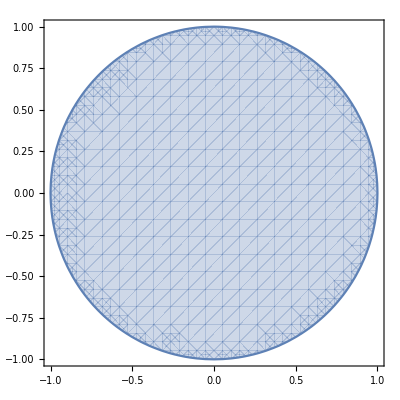

```mathematica
RegionPlot[x^2+y^2<=1,{x,-1,1},{y,-1,1}]
```

```mathematica
Hold[RegionPlot[x^2+y^2<=1,{x,-1,1},{y,-1,1}]]
```

Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]]

```mathematica
Extract[Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]],1,Hold]
```

Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]]

```mathematica
Extract[Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]],{1,1},Hold]
```

Hold[x^2+y^2≤1]

```mathematica
First[Extract[Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]],{1,1},Hold]]
```

x^2+y^2≤1

```mathematica
Boole[First[Extract[Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]],{1,1},Hold]]]
```

Boole[x^2+y^2≤1]

```mathematica
Integrate[Boole[First[Extract[Hold[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]],{1,1},Hold]]],{x,-1,1},{y,-1,1}]
```

π

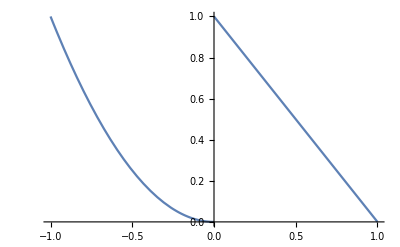

```mathematica
Plot[Piecewise[{{x^2,x<0},{1-x,x>0}}],{x,-1,1}]
```

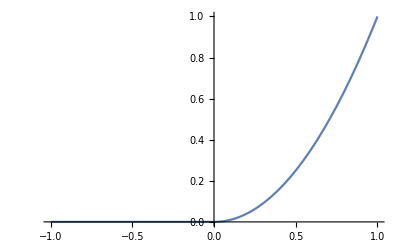

```mathematica
Plot[Piecewise[{{x^2, x>0}}],{x,-1,1}]
```

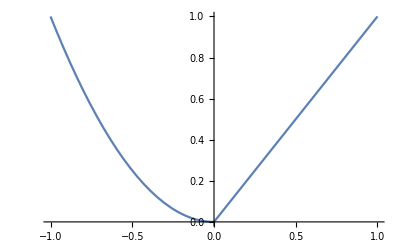

```mathematica
Plot[Piecewise[{{x^2, x<0}, {x, x>=0}}],{x,-1,1}]
```

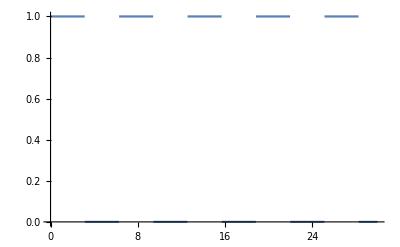

```mathematica
Plot[UnitStep[Sin[x]],{x,0,30}]
```

```mathematica
Integrate[UnitStep[Sin[x]],{x,0,30}]
```

5 π

### Random numbers

```mathematica
RandomInteger[]
```

1

```mathematica
RandomComplex[]
```

0.847348+0.261897 ⅈ

```mathematica
RandomInteger[{0,9},10]
```

{0,0,4,5,0,9,8,8,0,8}

```mathematica
RandomInteger[{0,9},100]
```

{8,0,8,4,4,3,7,3,0,3,1,4,0,6,6,9,1,6,9,9,7,4,4,7,9,0,1,3,4,0,7,8,1,2,6,6,2,8,3,0,1,8,4,1,8,8,4,4,7,8,8,0,6,0,7,7,0,0,3,1,9,4,2,9,1,0,7,9,2,1,3,2,0,6,6,6,9,4,0,5,4,0,0,2,7,4,9,0,3,4,1,0,3,0,6,0,6,1,0,4}

```mathematica
RandomInteger[{0,12},100]
```

{4,8,8,8,9,11,4,10,1,4,9,1,2,6,1,4,4,2,5,11,11,10,9,8,0,1,2,1,2,11,6,4,12,10,11,3,2,9,2,1,9,4,3,11,6,9,6,6,7,11,10,1,0,1,8,9,4,7,11,3,7,9,0,7,0,0,5,11,4,12,4,6,6,8,6,6,10,5,1,11,8,2,12,7,11,2,2,3,8,6,0,4,9,4,6,0,8,10,6,1}

```mathematica
RandomReal[1,{3,3}]
```

{{0.364708,0.234596,0.982168},{0.316452,0.760494,0.893188},{0.692619,0.515763,0.432489}}

```mathematica
RandomReal[WorkingPrecision->30]
```

0.0572490561177717552683938879979

```mathematica
RandomComplex[{-1-I,1+I},4,WorkingPrecision->20]
```

{-0.47104889961444925795-0.77193517357104825785 ⅈ,0.43636984670024218854+0.056742571222765569611 ⅈ,-0.89394773183478707081-0.055687181141177397124 ⅈ,-0.91947761836291564375+0.27414665282374714659 ⅈ}

```mathematica
Sqrt[x^2]==Abs[x]
```

√(x^2)==Abs[x]

```mathematica
Sqrt[x^2]==Abs[x]/.x->RandomComplex[]
```

False

```mathematica
SeedRandom[]
```

RandomGeneratorState[…]

```mathematica
RandomReal[1,{3}]
```

{0.926462,0.806267,0.23551}

```mathematica
SeedRandom[143];RandomReal[1,{3}]
```

{0.110762,0.364563,0.163681}

```mathematica
{BlockRandom[{RandomReal[],RandomReal[]}],{RandomReal[],RandomReal[]}}
```

{{0.753386,0.977218},{0.753386,0.977218}}

```mathematica
RandomInteger[PoissonDistribution[3],12]
```

{1,1,2,1,1,1,7,2,0,6,4,4}

```mathematica
RandomReal[NormalDistribution[],{4,4}]
```

{{1.26611,-2.31531,0.161556,-0.776826},{1.41742,1.24571,-1.2093,-0.0176764},{0.732085,0.308799,1.13969,-0.327573},{0.410081,-2.55579,0.761807,-1.38589}}

```mathematica
RandomReal[NormalDistribution[2,4],5,WorkingPrecision->32]
```

{-0.96859604504409918808552411133316,-1.5226435491212939030513850706567,1.622053902544193555060953951909,8.1932832420079471746120151622343,3.4059553866036510062976691475831}

```mathematica
RandomChoice[Random[0,9],10]
```

RandomChoice[Random[0,9],10]

```mathematica
RandomSample[Range[0,9],10]
```

{1,5,3,0,6,9,4,8,7,2}

```mathematica
RandomSample[{0,1,2,2,3,3,3,4,4,4,4,5,5,5,5,5,6,6,6,6,6,6,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9},10]
```

{8,9,8,1,5,4,9,4,8,0}